```mathematica
f[x_,θ_,k_]:=x^(k-1)*Exp[-x/θ]/θ^k/Gamma[k]
```

```mathematica
F[x_, θ_,n_]:=NIntegrate[f[t,θ,n],{t,0,x}]
```

```mathematica
1-F[10,1,10]
```

0.54207

```mathematica
Lambdaa[n_]:=InverseCDF[GammaDistribution[n, 1],0.95]
Lambdab[n_]:=InverseCDF[GammaDistribution[n, 1],0.05]
```

```mathematica
L[n_]:=2*Lambdab[n]-Lambdaa[n]
```

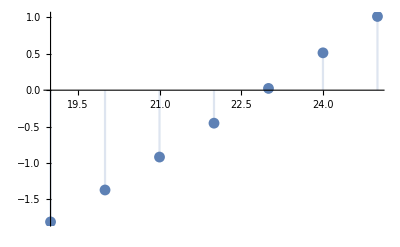

```mathematica
DiscretePlot[L[n],{n,19,25}]
```

```mathematica
Lambdaa[n_]:=FindRoot[CDF[GammaDistribution[n, 1],x]==0.95,{x,1}]
```

```mathematica
Lambdaa[1]
```

{x→2.99573}

```mathematica
InverseCDF[NormalDistribution[0, 1],0.5]
```

0.

```mathematica
L[22]
```

-0.452966

```mathematica
Integrate[Exp[-x/a]/a*x,{x,0,+Infinity}]
```

ConditionalExpression[a,Re[a]>0]